```mathematica
SetDirectory["C:\\Users\\Rafael\\Archivos\\Universidad\\Ciencias\\Fisica\\TecnicasBazo\\Proyecto\\Total"]
```

C:\Users\Rafael\Archivos\Universidad\Ciencias\Fisica\TecnicasBazo\Proyecto\Total

```mathematica
a=FileNames[{"T*.dat","Sc*.cfg"},{"TEMP*","VBB*"},2]
```

{TEMP_20\VBB_0\ScanConfig_160317_1624.cfg,TEMP_20\VBB_0\ScanConfig_160317_1637.cfg,TEMP_20\VBB_0\ScanConfig_160317_1649.cfg,TEMP_20\VBB_0\ScanConfig_160317_1716.cfg,TEMP_20\VBB_0\ScanConfig_160317_1728.cfg,TEMP_20\VBB_0\ScanConfig_160317_1753.cfg,TEMP_20\VBB_0\ScanConfig_160317_1805.cfg,TEMP_20\VBB_0\ScanConfig_160317_1825.cfg,TEMP_20\VBB_0\ScanConfig_160317_1837.cfg,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1624.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1637.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1649.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1716.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1728.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1753.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1805.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1825.dat,TEMP_20\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160317_1837.dat,TEMP_20\VBB_3\ScanConfig_160316_1504.cfg,TEMP_20\VBB_3\ScanConfig_160316_1517.cfg,TEMP_20\VBB_3\ScanConfig_160316_1530.cfg,TEMP_20\VBB_3\ScanConfig_160316_1542.cfg,TEMP_20\VBB_3\ScanConfig_160316_1555.cfg,TEMP_20\VBB_3\ScanConfig_160316_1608.cfg,TEMP_20\VBB_3\ScanConfig_160316_1620.cfg,TEMP_20\VBB_3\ScanConfig_160316_1633.cfg,TEMP_20\VBB_3\ScanConfig_160316_1646.cfg,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1504.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1517.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1530.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1542.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1555.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1608.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1620.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1633.dat,TEMP_20\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160316_1646.dat,TEMP_20\VBB_6\ScanConfig_160316_1701.cfg,TEMP_20\VBB_6\ScanConfig_160316_1714.cfg,TEMP_20\VBB_6\ScanConfig_160316_1726.cfg,TEMP_20\VBB_6\ScanConfig_160316_1739.cfg,TEMP_20\VBB_6\ScanConfig_160316_1751.cfg,TEMP_20\VBB_6\ScanConfig_160316_1804.cfg,TEMP_20\VBB_6\ScanConfig_160316_1816.cfg,TEMP_20\VBB_6\ScanConfig_160316_1828.cfg,TEMP_20\VBB_6\ScanConfig_160316_1840.cfg,TEMP_20\VBB_6\ScanConfig_160316_1852.cfg,TEMP_20\VBB_6\ScanConfig_160316_1904.cfg,TEMP_20\VBB_6\ScanConfig_160316_1916.cfg,TEMP_20\VBB_6\ScanConfig_160316_1928.cfg,TEMP_20\VBB_6\ScanConfig_160316_1940.cfg,TEMP_20\VBB_6\ScanConfig_160316_1952.cfg,TEMP_20\VBB_6\ScanConfig_160316_2004.cfg,TEMP_20\VBB_6\ScanConfig_160316_2016.cfg,TEMP_20\VBB_6\ScanConfig_160316_2028.cfg,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1701.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1714.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1726.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1739.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1751.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1804.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1816.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1828.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1840.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1852.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1904.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1916.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1928.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1940.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_1952.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_2004.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_2016.dat,TEMP_20\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_2028.dat,TEMP_25\VBB_0\ScanConfig_160314_1916.cfg,TEMP_25\VBB_0\ScanConfig_160314_1928.cfg,TEMP_25\VBB_0\ScanConfig_160314_1941.cfg,TEMP_25\VBB_0\ScanConfig_160314_1953.cfg,TEMP_25\VBB_0\ScanConfig_160314_2006.cfg,TEMP_25\VBB_0\ScanConfig_160314_2018.cfg,TEMP_25\VBB_0\ScanConfig_160314_2031.cfg,TEMP_25\VBB_0\ScanConfig_160314_2043.cfg,TEMP_25\VBB_0\ScanConfig_160314_2056.cfg,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_1916.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_1928.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_1941.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_1953.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_2006.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_2018.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_2031.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_2043.dat,TEMP_25\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160314_2056.dat,TEMP_25\VBB_1\ScanConfig_160315_1004.cfg,TEMP_25\VBB_1\ScanConfig_160315_1017.cfg,TEMP_25\VBB_1\ScanConfig_160315_1030.cfg,TEMP_25\VBB_1\ScanConfig_160315_1042.cfg,TEMP_25\VBB_1\ScanConfig_160315_1055.cfg,TEMP_25\VBB_1\ScanConfig_160315_1108.cfg,TEMP_25\VBB_1\ScanConfig_160315_1120.cfg,TEMP_25\VBB_1\ScanConfig_160315_1133.cfg,TEMP_25\VBB_1\ScanConfig_160315_1145.cfg,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1004.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1017.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1030.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1042.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1055.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1108.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1120.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1133.dat,TEMP_25\VBB_1\ThresholdScanByRandom_PixelsPerReg_500_160315_1145.dat,TEMP_25\VBB_2\ScanConfig_160315_1654.cfg,TEMP_25\VBB_2\ScanConfig_160315_1707.cfg,TEMP_25\VBB_2\ScanConfig_160315_1719.cfg,TEMP_25\VBB_2\ScanConfig_160315_1732.cfg,TEMP_25\VBB_2\ScanConfig_160315_1744.cfg,TEMP_25\VBB_2\ScanConfig_160315_1757.cfg,TEMP_25\VBB_2\ScanConfig_160315_1810.cfg,TEMP_25\VBB_2\ScanConfig_160315_1822.cfg,TEMP_25\VBB_2\ScanConfig_160315_1834.cfg,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1654.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1707.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1719.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1732.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1744.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1757.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1810.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1822.dat,TEMP_25\VBB_2\ThresholdScanByRandom_PixelsPerReg_500_160315_1834.dat,TEMP_25\VBB_3\ScanConfig_160315_1226.cfg,TEMP_25\VBB_3\ScanConfig_160315_1239.cfg,TEMP_25\VBB_3\ScanConfig_160315_1252.cfg,TEMP_25\VBB_3\ScanConfig_160315_1304.cfg,TEMP_25\VBB_3\ScanConfig_160315_1317.cfg,TEMP_25\VBB_3\ScanConfig_160315_1330.cfg,TEMP_25\VBB_3\ScanConfig_160315_1342.cfg,TEMP_25\VBB_3\ScanConfig_160315_1355.cfg,TEMP_25\VBB_3\ScanConfig_160315_1408.cfg,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1226.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1239.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1252.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1304.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1317.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1330.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1342.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1355.dat,TEMP_25\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160315_1408.dat,TEMP_25\VBB_4\ScanConfig_160316_1140.cfg,TEMP_25\VBB_4\ScanConfig_160316_1152.cfg,TEMP_25\VBB_4\ScanConfig_160316_1204.cfg,TEMP_25\VBB_4\ScanConfig_160316_1217.cfg,TEMP_25\VBB_4\ScanConfig_160316_1229.cfg,TEMP_25\VBB_4\ScanConfig_160316_1242.cfg,TEMP_25\VBB_4\ScanConfig_160316_1254.cfg,TEMP_25\VBB_4\ScanConfig_160316_1307.cfg,TEMP_25\VBB_4\ScanConfig_160316_1319.cfg,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1140.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1152.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1204.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1217.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1229.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1242.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1254.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1307.dat,TEMP_25\VBB_4\ThresholdScanByRandom_PixelsPerReg_500_160316_1319.dat,TEMP_25\VBB_5\ScanConfig_160316_0941.cfg,TEMP_25\VBB_5\ScanConfig_160316_0953.cfg,TEMP_25\VBB_5\ScanConfig_160316_1006.cfg,TEMP_25\VBB_5\ScanConfig_160316_1018.cfg,TEMP_25\VBB_5\ScanConfig_160316_1031.cfg,TEMP_25\VBB_5\ScanConfig_160316_1043.cfg,TEMP_25\VBB_5\ScanConfig_160316_1056.cfg,TEMP_25\VBB_5\ScanConfig_160316_1109.cfg,TEMP_25\VBB_5\ScanConfig_160316_1122.cfg,TEMP_25\VBB_5\ScanConfig_160317_2000.cfg,TEMP_25\VBB_5\ScanConfig_160317_2013.cfg,TEMP_25\VBB_5\ScanConfig_160317_2025.cfg,TEMP_25\VBB_5\ScanConfig_160317_2038.cfg,TEMP_25\VBB_5\ScanConfig_160317_2050.cfg,TEMP_25\VBB_5\ScanConfig_160317_2103.cfg,TEMP_25\VBB_5\ScanConfig_160317_2115.cfg,TEMP_25\VBB_5\ScanConfig_160317_2128.cfg,TEMP_25\VBB_5\ScanConfig_160317_2141.cfg,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_0941.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_0953.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1006.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1018.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1031.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1043.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1056.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1109.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160316_1122.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2000.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2013.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2025.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2038.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2050.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2103.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2115.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2128.dat,TEMP_25\VBB_5\ThresholdScanByRandom_PixelsPerReg_500_160317_2141.dat,TEMP_25\VBB_6\ScanConfig_160315_1855.cfg,TEMP_25\VBB_6\ScanConfig_160315_1907.cfg,TEMP_25\VBB_6\ScanConfig_160315_1920.cfg,TEMP_25\VBB_6\ScanConfig_160315_1932.cfg,TEMP_25\VBB_6\ScanConfig_160315_1945.cfg,TEMP_25\VBB_6\ScanConfig_160315_1957.cfg,TEMP_25\VBB_6\ScanConfig_160315_2010.cfg,TEMP_25\VBB_6\ScanConfig_160315_2022.cfg,TEMP_25\VBB_6\ScanConfig_160315_2035.cfg,TEMP_25\VBB_6\ScanConfig_160315_2048.cfg,TEMP_25\VBB_6\ScanConfig_160315_2059.cfg,TEMP_25\VBB_6\ScanConfig_160315_2111.cfg,TEMP_25\VBB_6\ScanConfig_160315_2123.cfg,TEMP_25\VBB_6\ScanConfig_160315_2135.cfg,TEMP_25\VBB_6\ScanConfig_160315_2147.cfg,TEMP_25\VBB_6\ScanConfig_160315_2159.cfg,TEMP_25\VBB_6\ScanConfig_160316_0856.cfg,TEMP_25\VBB_6\ScanConfig_160316_0909.cfg,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_1855.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_1907.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_1920.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_1932.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_1945.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_1957.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2010.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2022.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2035.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2048.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2059.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2111.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2123.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2135.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2147.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160315_2159.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_0856.dat,TEMP_25\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160316_0909.dat,TEMP_30\VBB_0\ScanConfig_160323_1131.cfg,TEMP_30\VBB_0\ScanConfig_160323_1143.cfg,TEMP_30\VBB_0\ScanConfig_160323_1156.cfg,TEMP_30\VBB_0\ScanConfig_160323_1208.cfg,TEMP_30\VBB_0\ScanConfig_160323_1221.cfg,TEMP_30\VBB_0\ScanConfig_160323_1233.cfg,TEMP_30\VBB_0\ScanConfig_160323_1246.cfg,TEMP_30\VBB_0\ScanConfig_160323_1258.cfg,TEMP_30\VBB_0\ScanConfig_160323_1311.cfg,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1131.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1143.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1156.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1208.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1221.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1233.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1246.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1258.dat,TEMP_30\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160323_1311.dat,TEMP_30\VBB_3\ScanConfig_160323_0921.cfg,TEMP_30\VBB_3\ScanConfig_160323_0934.cfg,TEMP_30\VBB_3\ScanConfig_160323_0946.cfg,TEMP_30\VBB_3\ScanConfig_160323_0958.cfg,TEMP_30\VBB_3\ScanConfig_160323_1011.cfg,TEMP_30\VBB_3\ScanConfig_160323_1023.cfg,TEMP_30\VBB_3\ScanConfig_160323_1035.cfg,TEMP_30\VBB_3\ScanConfig_160323_1048.cfg,TEMP_30\VBB_3\ScanConfig_160323_1100.cfg,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_0921.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_0934.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_0946.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_0958.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_1011.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_1023.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_1035.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_1048.dat,TEMP_30\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160323_1100.dat,TEMP_30\VBB_6\ScanConfig_160321_1000.cfg,TEMP_30\VBB_6\ScanConfig_160321_1012.cfg,TEMP_30\VBB_6\ScanConfig_160321_1025.cfg,TEMP_30\VBB_6\ScanConfig_160321_1037.cfg,TEMP_30\VBB_6\ScanConfig_160321_1049.cfg,TEMP_30\VBB_6\ScanConfig_160321_1102.cfg,TEMP_30\VBB_6\ScanConfig_160321_1114.cfg,TEMP_30\VBB_6\ScanConfig_160321_1126.cfg,TEMP_30\VBB_6\ScanConfig_160321_1139.cfg,TEMP_30\VBB_6\ScanConfig_160321_1151.cfg,TEMP_30\VBB_6\ScanConfig_160321_1203.cfg,TEMP_30\VBB_6\ScanConfig_160321_1215.cfg,TEMP_30\VBB_6\ScanConfig_160321_1228.cfg,TEMP_30\VBB_6\ScanConfig_160321_1240.cfg,TEMP_30\VBB_6\ScanConfig_160321_1252.cfg,TEMP_30\VBB_6\ScanConfig_160321_1305.cfg,TEMP_30\VBB_6\ScanConfig_160321_1317.cfg,TEMP_30\VBB_6\ScanConfig_160321_1329.cfg,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1000.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1012.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1025.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1037.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1049.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1102.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1114.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1126.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1139.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1151.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1203.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1215.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1228.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1240.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1252.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1305.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1317.dat,TEMP_30\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1329.dat,TEMP_35\VBB_0\ScanConfig_160329_1336.cfg,TEMP_35\VBB_0\ScanConfig_160329_1348.cfg,TEMP_35\VBB_0\ScanConfig_160329_1400.cfg,TEMP_35\VBB_0\ScanConfig_160329_1536.cfg,TEMP_35\VBB_0\ScanConfig_160329_1549.cfg,TEMP_35\VBB_0\ScanConfig_160329_1602.cfg,TEMP_35\VBB_0\ScanConfig_160329_1615.cfg,TEMP_35\VBB_0\ScanConfig_160329_1627.cfg,TEMP_35\VBB_0\ScanConfig_160329_1640.cfg,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1336.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1348.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1400.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1536.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1549.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1602.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1615.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1627.dat,TEMP_35\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160329_1640.dat,TEMP_35\VBB_3\ScanConfig_160321_1943.cfg,TEMP_35\VBB_3\ScanConfig_160321_1955.cfg,TEMP_35\VBB_3\ScanConfig_160321_2007.cfg,TEMP_35\VBB_3\ScanConfig_160321_2020.cfg,TEMP_35\VBB_3\ScanConfig_160321_2033.cfg,TEMP_35\VBB_3\ScanConfig_160321_2045.cfg,TEMP_35\VBB_3\ScanConfig_160321_2057.cfg,TEMP_35\VBB_3\ScanConfig_160321_2110.cfg,TEMP_35\VBB_3\ScanConfig_160321_2122.cfg,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_1943.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_1955.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2007.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2020.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2033.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2045.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2057.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2110.dat,TEMP_35\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160321_2122.dat,TEMP_35\VBB_6\ScanConfig_160321_1554.cfg,TEMP_35\VBB_6\ScanConfig_160321_1607.cfg,TEMP_35\VBB_6\ScanConfig_160321_1619.cfg,TEMP_35\VBB_6\ScanConfig_160321_1631.cfg,TEMP_35\VBB_6\ScanConfig_160321_1644.cfg,TEMP_35\VBB_6\ScanConfig_160321_1656.cfg,TEMP_35\VBB_6\ScanConfig_160321_1709.cfg,TEMP_35\VBB_6\ScanConfig_160321_1722.cfg,TEMP_35\VBB_6\ScanConfig_160321_1734.cfg,TEMP_35\VBB_6\ScanConfig_160321_1747.cfg,TEMP_35\VBB_6\ScanConfig_160321_1759.cfg,TEMP_35\VBB_6\ScanConfig_160321_1812.cfg,TEMP_35\VBB_6\ScanConfig_160321_1824.cfg,TEMP_35\VBB_6\ScanConfig_160321_1837.cfg,TEMP_35\VBB_6\ScanConfig_160321_1849.cfg,TEMP_35\VBB_6\ScanConfig_160321_1902.cfg,TEMP_35\VBB_6\ScanConfig_160321_1914.cfg,TEMP_35\VBB_6\ScanConfig_160321_1927.cfg,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1554.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1607.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1619.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1631.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1644.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1656.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1709.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1722.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1734.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1747.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1759.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1812.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1824.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1837.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1849.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1902.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1914.dat,TEMP_35\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160321_1927.dat,TEMP_40\VBB_0\ScanConfig_160328_1411.cfg,TEMP_40\VBB_0\ScanConfig_160328_1423.cfg,TEMP_40\VBB_0\ScanConfig_160328_1436.cfg,TEMP_40\VBB_0\ScanConfig_160328_1448.cfg,TEMP_40\VBB_0\ScanConfig_160328_1501.cfg,TEMP_40\VBB_0\ScanConfig_160328_1513.cfg,TEMP_40\VBB_0\ScanConfig_160328_1526.cfg,TEMP_40\VBB_0\ScanConfig_160328_1538.cfg,TEMP_40\VBB_0\ScanConfig_160328_1551.cfg,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1411.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1423.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1436.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1448.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1501.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1513.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1526.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1538.dat,TEMP_40\VBB_0\ThresholdScanByRandom_PixelsPerReg_500_160328_1551.dat,TEMP_40\VBB_3\ScanConfig_160322_1716.cfg,TEMP_40\VBB_3\ScanConfig_160322_1729.cfg,TEMP_40\VBB_3\ScanConfig_160322_1741.cfg,TEMP_40\VBB_3\ScanConfig_160322_1754.cfg,TEMP_40\VBB_3\ScanConfig_160322_1807.cfg,TEMP_40\VBB_3\ScanConfig_160322_1819.cfg,TEMP_40\VBB_3\ScanConfig_160322_1832.cfg,TEMP_40\VBB_3\ScanConfig_160322_1845.cfg,TEMP_40\VBB_3\ScanConfig_160322_1857.cfg,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1716.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1729.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1741.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1754.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1807.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1819.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1832.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1845.dat,TEMP_40\VBB_3\ThresholdScanByRandom_PixelsPerReg_500_160322_1857.dat,TEMP_40\VBB_6\ScanConfig_160322_1325.cfg,TEMP_40\VBB_6\ScanConfig_160322_1338.cfg,TEMP_40\VBB_6\ScanConfig_160322_1350.cfg,TEMP_40\VBB_6\ScanConfig_160322_1403.cfg,TEMP_40\VBB_6\ScanConfig_160322_1415.cfg,TEMP_40\VBB_6\ScanConfig_160322_1428.cfg,TEMP_40\VBB_6\ScanConfig_160322_1440.cfg,TEMP_40\VBB_6\ScanConfig_160322_1453.cfg,TEMP_40\VBB_6\ScanConfig_160322_1506.cfg,TEMP_40\VBB_6\ScanConfig_160322_1518.cfg,TEMP_40\VBB_6\ScanConfig_160322_1531.cfg,TEMP_40\VBB_6\ScanConfig_160322_1543.cfg,TEMP_40\VBB_6\ScanConfig_160322_1556.cfg,TEMP_40\VBB_6\ScanConfig_160322_1608.cfg,TEMP_40\VBB_6\ScanConfig_160322_1621.cfg,TEMP_40\VBB_6\ScanConfig_160322_1634.cfg,TEMP_40\VBB_6\ScanConfig_160322_1646.cfg,TEMP_40\VBB_6\ScanConfig_160322_1659.cfg,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1325.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1338.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1350.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1403.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1415.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1428.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1440.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1453.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1506.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1518.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1531.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1543.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1556.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1608.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1621.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1634.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1646.dat,TEMP_40\VBB_6\ThresholdScanByRandom_PixelsPerReg_500_160322_1659.dat}

```mathematica
b=StringSplit[#,","]&/@SplitBy [StringReplace[a,{x__~~"S"~~__~~"Config_"~~y__~~".cfg":>x~~","~~y,x__~~"Thres"~~__~~"500_"~~y__~~".dat":>x~~","~~y}]//DeleteDuplicates,First[StringSplit[#,","]]&]
```

{{{TEMP_20\VBB_0\,160317_1624},{TEMP_20\VBB_0\,160317_1637},{TEMP_20\VBB_0\,160317_1649},{TEMP_20\VBB_0\,160317_1716},{TEMP_20\VBB_0\,160317_1728},{TEMP_20\VBB_0\,160317_1753},{TEMP_20\VBB_0\,160317_1805},{TEMP_20\VBB_0\,160317_1825},{TEMP_20\VBB_0\,160317_1837}},{{TEMP_20\VBB_3\,160316_1504},{TEMP_20\VBB_3\,160316_1517},{TEMP_20\VBB_3\,160316_1530},{TEMP_20\VBB_3\,160316_1542},{TEMP_20\VBB_3\,160316_1555},{TEMP_20\VBB_3\,160316_1608},{TEMP_20\VBB_3\,160316_1620},{TEMP_20\VBB_3\,160316_1633},{TEMP_20\VBB_3\,160316_1646}},{{TEMP_20\VBB_6\,160316_1701},{TEMP_20\VBB_6\,160316_1714},{TEMP_20\VBB_6\,160316_1726},{TEMP_20\VBB_6\,160316_1739},{TEMP_20\VBB_6\,160316_1751},{TEMP_20\VBB_6\,160316_1804},{TEMP_20\VBB_6\,160316_1816},{TEMP_20\VBB_6\,160316_1828},{TEMP_20\VBB_6\,160316_1840},{TEMP_20\VBB_6\,160316_1852},{TEMP_20\VBB_6\,160316_1904},{TEMP_20\VBB_6\,160316_1916},{TEMP_20\VBB_6\,160316_1928},{TEMP_20\VBB_6\,160316_1940},{TEMP_20\VBB_6\,160316_1952},{TEMP_20\VBB_6\,160316_2004},{TEMP_20\VBB_6\,160316_2016},{TEMP_20\VBB_6\,160316_2028}},{{TEMP_25\VBB_0\,160314_1916},{TEMP_25\VBB_0\,160314_1928},{TEMP_25\VBB_0\,160314_1941},{TEMP_25\VBB_0\,160314_1953},{TEMP_25\VBB_0\,160314_2006},{TEMP_25\VBB_0\,160314_2018},{TEMP_25\VBB_0\,160314_2031},{TEMP_25\VBB_0\,160314_2043},{TEMP_25\VBB_0\,160314_2056}},{{TEMP_25\VBB_1\,160315_1004},{TEMP_25\VBB_1\,160315_1017},{TEMP_25\VBB_1\,160315_1030},{TEMP_25\VBB_1\,160315_1042},{TEMP_25\VBB_1\,160315_1055},{TEMP_25\VBB_1\,160315_1108},{TEMP_25\VBB_1\,160315_1120},{TEMP_25\VBB_1\,160315_1133},{TEMP_25\VBB_1\,160315_1145}},{{TEMP_25\VBB_2\,160315_1654},{TEMP_25\VBB_2\,160315_1707},{TEMP_25\VBB_2\,160315_1719},{TEMP_25\VBB_2\,160315_1732},{TEMP_25\VBB_2\,160315_1744},{TEMP_25\VBB_2\,160315_1757},{TEMP_25\VBB_2\,160315_1810},{TEMP_25\VBB_2\,160315_1822},{TEMP_25\VBB_2\,160315_1834}},{{TEMP_25\VBB_3\,160315_1226},{TEMP_25\VBB_3\,160315_1239},{TEMP_25\VBB_3\,160315_1252},{TEMP_25\VBB_3\,160315_1304},{TEMP_25\VBB_3\,160315_1317},{TEMP_25\VBB_3\,160315_1330},{TEMP_25\VBB_3\,160315_1342},{TEMP_25\VBB_3\,160315_1355},{TEMP_25\VBB_3\,160315_1408}},{{TEMP_25\VBB_4\,160316_1140},{TEMP_25\VBB_4\,160316_1152},{TEMP_25\VBB_4\,160316_1204},{TEMP_25\VBB_4\,160316_1217},{TEMP_25\VBB_4\,160316_1229},{TEMP_25\VBB_4\,160316_1242},{TEMP_25\VBB_4\,160316_1254},{TEMP_25\VBB_4\,160316_1307},{TEMP_25\VBB_4\,160316_1319}},{{TEMP_25\VBB_5\,160316_0941},{TEMP_25\VBB_5\,160316_0953},{TEMP_25\VBB_5\,160316_1006},{TEMP_25\VBB_5\,160316_1018},{TEMP_25\VBB_5\,160316_1031},{TEMP_25\VBB_5\,160316_1043},{TEMP_25\VBB_5\,160316_1056},{TEMP_25\VBB_5\,160316_1109},{TEMP_25\VBB_5\,160316_1122},{TEMP_25\VBB_5\,160317_2000},{TEMP_25\VBB_5\,160317_2013},{TEMP_25\VBB_5\,160317_2025},{TEMP_25\VBB_5\,160317_2038},{TEMP_25\VBB_5\,160317_2050},{TEMP_25\VBB_5\,160317_2103},{TEMP_25\VBB_5\,160317_2115},{TEMP_25\VBB_5\,160317_2128},{TEMP_25\VBB_5\,160317_2141}},{{TEMP_25\VBB_6\,160315_1855},{TEMP_25\VBB_6\,160315_1907},{TEMP_25\VBB_6\,160315_1920},{TEMP_25\VBB_6\,160315_1932},{TEMP_25\VBB_6\,160315_1945},{TEMP_25\VBB_6\,160315_1957},{TEMP_25\VBB_6\,160315_2010},{TEMP_25\VBB_6\,160315_2022},{TEMP_25\VBB_6\,160315_2035},{TEMP_25\VBB_6\,160315_2048},{TEMP_25\VBB_6\,160315_2059},{TEMP_25\VBB_6\,160315_2111},{TEMP_25\VBB_6\,160315_2123},{TEMP_25\VBB_6\,160315_2135},{TEMP_25\VBB_6\,160315_2147},{TEMP_25\VBB_6\,160315_2159},{TEMP_25\VBB_6\,160316_0856},{TEMP_25\VBB_6\,160316_0909}},{{TEMP_30\VBB_0\,160323_1131},{TEMP_30\VBB_0\,160323_1143},{TEMP_30\VBB_0\,160323_1156},{TEMP_30\VBB_0\,160323_1208},{TEMP_30\VBB_0\,160323_1221},{TEMP_30\VBB_0\,160323_1233},{TEMP_30\VBB_0\,160323_1246},{TEMP_30\VBB_0\,160323_1258},{TEMP_30\VBB_0\,160323_1311}},{{TEMP_30\VBB_3\,160323_0921},{TEMP_30\VBB_3\,160323_0934},{TEMP_30\VBB_3\,160323_0946},{TEMP_30\VBB_3\,160323_0958},{TEMP_30\VBB_3\,160323_1011},{TEMP_30\VBB_3\,160323_1023},{TEMP_30\VBB_3\,160323_1035},{TEMP_30\VBB_3\,160323_1048},{TEMP_30\VBB_3\,160323_1100}},{{TEMP_30\VBB_6\,160321_1000},{TEMP_30\VBB_6\,160321_1012},{TEMP_30\VBB_6\,160321_1025},{TEMP_30\VBB_6\,160321_1037},{TEMP_30\VBB_6\,160321_1049},{TEMP_30\VBB_6\,160321_1102},{TEMP_30\VBB_6\,160321_1114},{TEMP_30\VBB_6\,160321_1126},{TEMP_30\VBB_6\,160321_1139},{TEMP_30\VBB_6\,160321_1151},{TEMP_30\VBB_6\,160321_1203},{TEMP_30\VBB_6\,160321_1215},{TEMP_30\VBB_6\,160321_1228},{TEMP_30\VBB_6\,160321_1240},{TEMP_30\VBB_6\,160321_1252},{TEMP_30\VBB_6\,160321_1305},{TEMP_30\VBB_6\,160321_1317},{TEMP_30\VBB_6\,160321_1329}},{{TEMP_35\VBB_0\,160329_1336},{TEMP_35\VBB_0\,160329_1348},{TEMP_35\VBB_0\,160329_1400},{TEMP_35\VBB_0\,160329_1536},{TEMP_35\VBB_0\,160329_1549},{TEMP_35\VBB_0\,160329_1602},{TEMP_35\VBB_0\,160329_1615},{TEMP_35\VBB_0\,160329_1627},{TEMP_35\VBB_0\,160329_1640}},{{TEMP_35\VBB_3\,160321_1943},{TEMP_35\VBB_3\,160321_1955},{TEMP_35\VBB_3\,160321_2007},{TEMP_35\VBB_3\,160321_2020},{TEMP_35\VBB_3\,160321_2033},{TEMP_35\VBB_3\,160321_2045},{TEMP_35\VBB_3\,160321_2057},{TEMP_35\VBB_3\,160321_2110},{TEMP_35\VBB_3\,160321_2122}},{{TEMP_35\VBB_6\,160321_1554},{TEMP_35\VBB_6\,160321_1607},{TEMP_35\VBB_6\,160321_1619},{TEMP_35\VBB_6\,160321_1631},{TEMP_35\VBB_6\,160321_1644},{TEMP_35\VBB_6\,160321_1656},{TEMP_35\VBB_6\,160321_1709},{TEMP_35\VBB_6\,160321_1722},{TEMP_35\VBB_6\,160321_1734},{TEMP_35\VBB_6\,160321_1747},{TEMP_35\VBB_6\,160321_1759},{TEMP_35\VBB_6\,160321_1812},{TEMP_35\VBB_6\,160321_1824},{TEMP_35\VBB_6\,160321_1837},{TEMP_35\VBB_6\,160321_1849},{TEMP_35\VBB_6\,160321_1902},{TEMP_35\VBB_6\,160321_1914},{TEMP_35\VBB_6\,160321_1927}},{{TEMP_40\VBB_0\,160328_1411},{TEMP_40\VBB_0\,160328_1423},{TEMP_40\VBB_0\,160328_1436},{TEMP_40\VBB_0\,160328_1448},{TEMP_40\VBB_0\,160328_1501},{TEMP_40\VBB_0\,160328_1513},{TEMP_40\VBB_0\,160328_1526},{TEMP_40\VBB_0\,160328_1538},{TEMP_40\VBB_0\,160328_1551}},{{TEMP_40\VBB_3\,160322_1716},{TEMP_40\VBB_3\,160322_1729},{TEMP_40\VBB_3\,160322_1741},{TEMP_40\VBB_3\,160322_1754},{TEMP_40\VBB_3\,160322_1807},{TEMP_40\VBB_3\,160322_1819},{TEMP_40\VBB_3\,160322_1832},{TEMP_40\VBB_3\,160322_1845},{TEMP_40\VBB_3\,160322_1857}},{{TEMP_40\VBB_6\,160322_1325},{TEMP_40\VBB_6\,160322_1338},{TEMP_40\VBB_6\,160322_1350},{TEMP_40\VBB_6\,160322_1403},{TEMP_40\VBB_6\,160322_1415},{TEMP_40\VBB_6\,160322_1428},{TEMP_40\VBB_6\,160322_1440},{TEMP_40\VBB_6\,160322_1453},{TEMP_40\VBB_6\,160322_1506},{TEMP_40\VBB_6\,160322_1518},{TEMP_40\VBB_6\,160322_1531},{TEMP_40\VBB_6\,160322_1543},{TEMP_40\VBB_6\,160322_1556},{TEMP_40\VBB_6\,160322_1608},{TEMP_40\VBB_6\,160322_1621},{TEMP_40\VBB_6\,160322_1634},{TEMP_40\VBB_6\,160322_1646},{TEMP_40\VBB_6\,160322_1659}}}

```mathematica
Sequence@@b[[1,1,{1,2}]]
```

Sequence[TEMP_20\VBB_0\,160317_1624]

```mathematica
Directory[]
```

C:\Users\Rafael\Archivos\Universidad\Ciencias\Fisica\TecnicasBazo\Proyecto\Total

```mathematica
b//Flatten//Length
```

450

```mathematica
Flatten[b,1]
```

{{TEMP_20\VBB_0\,160317_1624},{TEMP_20\VBB_0\,160317_1637},{TEMP_20\VBB_0\,160317_1649},{TEMP_20\VBB_0\,160317_1716},{TEMP_20\VBB_0\,160317_1728},{TEMP_20\VBB_0\,160317_1753},{TEMP_20\VBB_0\,160317_1805},{TEMP_20\VBB_0\,160317_1825},{TEMP_20\VBB_0\,160317_1837},{TEMP_20\VBB_3\,160316_1504},{TEMP_20\VBB_3\,160316_1517},{TEMP_20\VBB_3\,160316_1530},{TEMP_20\VBB_3\,160316_1542},{TEMP_20\VBB_3\,160316_1555},{TEMP_20\VBB_3\,160316_1608},{TEMP_20\VBB_3\,160316_1620},{TEMP_20\VBB_3\,160316_1633},{TEMP_20\VBB_3\,160316_1646},{TEMP_20\VBB_6\,160316_1701},{TEMP_20\VBB_6\,160316_1714},{TEMP_20\VBB_6\,160316_1726},{TEMP_20\VBB_6\,160316_1739},{TEMP_20\VBB_6\,160316_1751},{TEMP_20\VBB_6\,160316_1804},{TEMP_20\VBB_6\,160316_1816},{TEMP_20\VBB_6\,160316_1828},{TEMP_20\VBB_6\,160316_1840},{TEMP_20\VBB_6\,160316_1852},{TEMP_20\VBB_6\,160316_1904},{TEMP_20\VBB_6\,160316_1916},{TEMP_20\VBB_6\,160316_1928},{TEMP_20\VBB_6\,160316_1940},{TEMP_20\VBB_6\,160316_1952},{TEMP_20\VBB_6\,160316_2004},{TEMP_20\VBB_6\,160316_2016},{TEMP_20\VBB_6\,160316_2028},{TEMP_25\VBB_0\,160314_1916},{TEMP_25\VBB_0\,160314_1928},{TEMP_25\VBB_0\,160314_1941},{TEMP_25\VBB_0\,160314_1953},{TEMP_25\VBB_0\,160314_2006},{TEMP_25\VBB_0\,160314_2018},{TEMP_25\VBB_0\,160314_2031},{TEMP_25\VBB_0\,160314_2043},{TEMP_25\VBB_0\,160314_2056},{TEMP_25\VBB_1\,160315_1004},{TEMP_25\VBB_1\,160315_1017},{TEMP_25\VBB_1\,160315_1030},{TEMP_25\VBB_1\,160315_1042},{TEMP_25\VBB_1\,160315_1055},{TEMP_25\VBB_1\,160315_1108},{TEMP_25\VBB_1\,160315_1120},{TEMP_25\VBB_1\,160315_1133},{TEMP_25\VBB_1\,160315_1145},{TEMP_25\VBB_2\,160315_1654},{TEMP_25\VBB_2\,160315_1707},{TEMP_25\VBB_2\,160315_1719},{TEMP_25\VBB_2\,160315_1732},{TEMP_25\VBB_2\,160315_1744},{TEMP_25\VBB_2\,160315_1757},{TEMP_25\VBB_2\,160315_1810},{TEMP_25\VBB_2\,160315_1822},{TEMP_25\VBB_2\,160315_1834},{TEMP_25\VBB_3\,160315_1226},{TEMP_25\VBB_3\,160315_1239},{TEMP_25\VBB_3\,160315_1252},{TEMP_25\VBB_3\,160315_1304},{TEMP_25\VBB_3\,160315_1317},{TEMP_25\VBB_3\,160315_1330},{TEMP_25\VBB_3\,160315_1342},{TEMP_25\VBB_3\,160315_1355},{TEMP_25\VBB_3\,160315_1408},{TEMP_25\VBB_4\,160316_1140},{TEMP_25\VBB_4\,160316_1152},{TEMP_25\VBB_4\,160316_1204},{TEMP_25\VBB_4\,160316_1217},{TEMP_25\VBB_4\,160316_1229},{TEMP_25\VBB_4\,160316_1242},{TEMP_25\VBB_4\,160316_1254},{TEMP_25\VBB_4\,160316_1307},{TEMP_25\VBB_4\,160316_1319},{TEMP_25\VBB_5\,160316_0941},{TEMP_25\VBB_5\,160316_0953},{TEMP_25\VBB_5\,160316_1006},{TEMP_25\VBB_5\,160316_1018},{TEMP_25\VBB_5\,160316_1031},{TEMP_25\VBB_5\,160316_1043},{TEMP_25\VBB_5\,160316_1056},{TEMP_25\VBB_5\,160316_1109},{TEMP_25\VBB_5\,160316_1122},{TEMP_25\VBB_5\,160317_2000},{TEMP_25\VBB_5\,160317_2013},{TEMP_25\VBB_5\,160317_2025},{TEMP_25\VBB_5\,160317_2038},{TEMP_25\VBB_5\,160317_2050},{TEMP_25\VBB_5\,160317_2103},{TEMP_25\VBB_5\,160317_2115},{TEMP_25\VBB_5\,160317_2128},{TEMP_25\VBB_5\,160317_2141},{TEMP_25\VBB_6\,160315_1855},{TEMP_25\VBB_6\,160315_1907},{TEMP_25\VBB_6\,160315_1920},{TEMP_25\VBB_6\,160315_1932},{TEMP_25\VBB_6\,160315_1945},{TEMP_25\VBB_6\,160315_1957},{TEMP_25\VBB_6\,160315_2010},{TEMP_25\VBB_6\,160315_2022},{TEMP_25\VBB_6\,160315_2035},{TEMP_25\VBB_6\,160315_2048},{TEMP_25\VBB_6\,160315_2059},{TEMP_25\VBB_6\,160315_2111},{TEMP_25\VBB_6\,160315_2123},{TEMP_25\VBB_6\,160315_2135},{TEMP_25\VBB_6\,160315_2147},{TEMP_25\VBB_6\,160315_2159},{TEMP_25\VBB_6\,160316_0856},{TEMP_25\VBB_6\,160316_0909},{TEMP_30\VBB_0\,160323_1131},{TEMP_30\VBB_0\,160323_1143},{TEMP_30\VBB_0\,160323_1156},{TEMP_30\VBB_0\,160323_1208},{TEMP_30\VBB_0\,160323_1221},{TEMP_30\VBB_0\,160323_1233},{TEMP_30\VBB_0\,160323_1246},{TEMP_30\VBB_0\,160323_1258},{TEMP_30\VBB_0\,160323_1311},{TEMP_30\VBB_3\,160323_0921},{TEMP_30\VBB_3\,160323_0934},{TEMP_30\VBB_3\,160323_0946},{TEMP_30\VBB_3\,160323_0958},{TEMP_30\VBB_3\,160323_1011},{TEMP_30\VBB_3\,160323_1023},{TEMP_30\VBB_3\,160323_1035},{TEMP_30\VBB_3\,160323_1048},{TEMP_30\VBB_3\,160323_1100},{TEMP_30\VBB_6\,160321_1000},{TEMP_30\VBB_6\,160321_1012},{TEMP_30\VBB_6\,160321_1025},{TEMP_30\VBB_6\,160321_1037},{TEMP_30\VBB_6\,160321_1049},{TEMP_30\VBB_6\,160321_1102},{TEMP_30\VBB_6\,160321_1114},{TEMP_30\VBB_6\,160321_1126},{TEMP_30\VBB_6\,160321_1139},{TEMP_30\VBB_6\,160321_1151},{TEMP_30\VBB_6\,160321_1203},{TEMP_30\VBB_6\,160321_1215},{TEMP_30\VBB_6\,160321_1228},{TEMP_30\VBB_6\,160321_1240},{TEMP_30\VBB_6\,160321_1252},{TEMP_30\VBB_6\,160321_1305},{TEMP_30\VBB_6\,160321_1317},{TEMP_30\VBB_6\,160321_1329},{TEMP_35\VBB_0\,160329_1336},{TEMP_35\VBB_0\,160329_1348},{TEMP_35\VBB_0\,160329_1400},{TEMP_35\VBB_0\,160329_1536},{TEMP_35\VBB_0\,160329_1549},{TEMP_35\VBB_0\,160329_1602},{TEMP_35\VBB_0\,160329_1615},{TEMP_35\VBB_0\,160329_1627},{TEMP_35\VBB_0\,160329_1640},{TEMP_35\VBB_3\,160321_1943},{TEMP_35\VBB_3\,160321_1955},{TEMP_35\VBB_3\,160321_2007},{TEMP_35\VBB_3\,160321_2020},{TEMP_35\VBB_3\,160321_2033},{TEMP_35\VBB_3\,160321_2045},{TEMP_35\VBB_3\,160321_2057},{TEMP_35\VBB_3\,160321_2110},{TEMP_35\VBB_3\,160321_2122},{TEMP_35\VBB_6\,160321_1554},{TEMP_35\VBB_6\,160321_1607},{TEMP_35\VBB_6\,160321_1619},{TEMP_35\VBB_6\,160321_1631},{TEMP_35\VBB_6\,160321_1644},{TEMP_35\VBB_6\,160321_1656},{TEMP_35\VBB_6\,160321_1709},{TEMP_35\VBB_6\,160321_1722},{TEMP_35\VBB_6\,160321_1734},{TEMP_35\VBB_6\,160321_1747},{TEMP_35\VBB_6\,160321_1759},{TEMP_35\VBB_6\,160321_1812},{TEMP_35\VBB_6\,160321_1824},{TEMP_35\VBB_6\,160321_1837},{TEMP_35\VBB_6\,160321_1849},{TEMP_35\VBB_6\,160321_1902},{TEMP_35\VBB_6\,160321_1914},{TEMP_35\VBB_6\,160321_1927},{TEMP_40\VBB_0\,160328_1411},{TEMP_40\VBB_0\,160328_1423},{TEMP_40\VBB_0\,160328_1436},{TEMP_40\VBB_0\,160328_1448},{TEMP_40\VBB_0\,160328_1501},{TEMP_40\VBB_0\,160328_1513},{TEMP_40\VBB_0\,160328_1526},{TEMP_40\VBB_0\,160328_1538},{TEMP_40\VBB_0\,160328_1551},{TEMP_40\VBB_3\,160322_1716},{TEMP_40\VBB_3\,160322_1729},{TEMP_40\VBB_3\,160322_1741},{TEMP_40\VBB_3\,160322_1754},{TEMP_40\VBB_3\,160322_1807},{TEMP_40\VBB_3\,160322_1819},{TEMP_40\VBB_3\,160322_1832},{TEMP_40\VBB_3\,160322_1845},{TEMP_40\VBB_3\,160322_1857},{TEMP_40\VBB_6\,160322_1325},{TEMP_40\VBB_6\,160322_1338},{TEMP_40\VBB_6\,160322_1350},{TEMP_40\VBB_6\,160322_1403},{TEMP_40\VBB_6\,160322_1415},{TEMP_40\VBB_6\,160322_1428},{TEMP_40\VBB_6\,160322_1440},{TEMP_40\VBB_6\,160322_1453},{TEMP_40\VBB_6\,160322_1506},{TEMP_40\VBB_6\,160322_1518},{TEMP_40\VBB_6\,160322_1531},{TEMP_40\VBB_6\,160322_1543},{TEMP_40\VBB_6\,160322_1556},{TEMP_40\VBB_6\,160322_1608},{TEMP_40\VBB_6\,160322_1621},{TEMP_40\VBB_6\,160322_1634},{TEMP_40\VBB_6\,160322_1646},{TEMP_40\VBB_6\,160322_1659}}

```mathematica
Length[Flatten[b,1]]
```

225

```mathematica
str=OpenWrite["./test.dat"]
```

OutputStream[./test.dat,175]

```mathematica
Do[Write[str,Sequence@@Flatten[b,1][[i,{1,2}]]],{i,1,Length[Flatten[b,1]]}]
```

```mathematica
Close[str]
```

./test.dat

```mathematica
SetDirectory["C:\\Users\\Rafael\\Archivos\\Universidad\\Ciencias\\Fisica\\TecnicasBazo\\Proyecto"]
```

C:\Users\Rafael\Archivos\Universidad\Ciencias\Fisica\TecnicasBazo\Proyecto

```mathematica
dat=Import["./outputtest0.dat","Data"];
```

```mathematica
Length[dat]
```

1048572

```mathematica
res1=((Partition[#,256][[{2,3}]]//Transpose)&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]);
```

```mathematica
res2=((Partition[#,256][[{1,3}]]//Transpose)&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]);
```

```mathematica
res1[[1]]
```

{{{256,0,38.4328,25.},{512,0,39.3187,25.}},{{257,0,31.9191,25.},{513,0,45.9336,25.}},{{258,0,36.,25.},{514,0,41.4982,25.}},{{259,0,39.9181,25.},{515,0,42.,25.}},{{260,0,37.2055,25.},{516,0,43.785,25.}},{{261,0,33.,25.},{517,0,42.2908,25.}},{{262,0,32.9467,25.},{518,0,45.7973,25.}},{{263,0,34.0918,25.},{519,0,46.5686,25.}},{{264,0,35.654,25.},{520,0,44.8176,25.}},{{265,0,34.7793,25.},{521,0,44.6057,25.}},{{266,0,36.,25.},{522,0,40.1264,25.}},{{267,0,29.6135,25.},{523,0,44.6398,25.}},{{268,0,34.5126,25.},{524,0,44.1954,25.}},{{269,0,37.0638,25.},{525,0,41.0515,25.}},{{270,0,39.4811,25.},{526,0,41.7081,25.}},{{271,0,34.8469,25.},{527,0,44.9438,25.}},{{272,0,32.5322,25.},{528,0,41.5964,25.}},{{273,0,33.6507,25.},{529,0,45.8649,25.}},{{274,0,34.7403,25.},{530,0,44.426,25.}},{{275,0,35.6186,25.},{531,0,39.9352,25.}},{{276,0,35.6079,25.},{532,0,41.2395,25.}},{{277,0,36.4074,25.},{533,0,44.8853,25.}},{{278,0,37.5246,25.},{534,0,41.7944,25.}},{{279,0,31.921,25.},{535,0,42.5438,25.}},{{280,0,35.196,25.},{536,0,42.1468,25.}},{{281,0,34.9372,25.},{537,0,39.3191,25.}},{{282,0,38.7733,25.},{538,0,42.6782,25.}},{{283,0,34.8311,25.},{539,0,40.9384,25.}},{{284,0,30.0886,25.},{540,0,44.5049,25.}},{{285,0,35.7098,25.},{541,0,44.5957,25.}},{{286,0,33.6624,25.},{542,0,44.9446,25.}},{{287,0,35.,25.},{543,0,39.0616,25.}},{{288,0,28.9368,25.},{544,0,43.7547,25.}},{{289,0,34.376,25.},{545,0,41.5543,25.}},{{290,0,31.4258,25.},{546,0,42.9111,25.}},{{291,0,33.4804,25.},{547,0,42.5172,25.}},{{292,0,33.4115,25.},{548,0,42.2188,25.}},{{293,0,34.8896,25.},{549,0,45.5483,25.}},{{294,0,36.374,25.},{550,0,40.944,25.}},{{295,0,36.5719,25.},{551,0,45.061,25.}},{{296,0,33.,25.},{552,0,37.8011,25.}},{{297,0,33.4882,25.},{553,0,42.5187,25.}},{{298,0,35.6136,25.},{554,0,38.3838,25.}},{{299,0,33.468,25.},{555,0,39.2617,25.}},{{300,0,35.8392,25.},{556,0,41.8377,25.}},{{301,0,33.4058,25.},{557,0,39.5002,25.}},{{302,0,31.9409,25.},{558,0,45.3106,25.}},{{303,0,33.7051,25.},{559,0,39.245,25.}},{{304,0,34.4173,25.},{560,0,42.4101,25.}},{{305,0,31.812,25.},{561,0,41.,25.}},{{306,0,30.4874,25.},{562,0,43.4341,25.}},{{307,0,34.4394,25.},{563,0,38.1544,25.}},{{308,0,34.4783,25.},{564,0,44.5967,25.}},{{309,0,34.4269,25.},{565,0,39.7855,25.}},{{310,0,29.7753,25.},{566,0,45.3169,25.}},{{311,0,36.3501,25.},{567,0,39.7189,25.}},{{312,0,36.904,25.},{568,0,45.0728,25.}},{{313,0,32.9111,25.},{569,0,44.3272,25.}},{{314,0,36.3724,25.},{570,0,45.7438,25.}},{{315,0,33.7601,25.},{571,0,45.9529,25.}},{{316,0,35.6355,25.},{572,0,41.9441,25.}},{{317,0,30.7415,25.},{573,0,44.7505,25.}},{{318,0,35.5506,25.},{574,0,42.4626,25.}},{{319,0,33.6424,25.},{575,0,46.0887,25.}},{{320,0,32.,25.},{576,0,39.6139,25.}},{{321,0,34.2992,25.},{577,0,41.9039,25.}},{{322,0,29.7317,25.},{578,0,41.9103,25.}},{{323,0,36.646,25.},{579,0,41.1873,25.}},{{324,0,35.0564,25.},{580,0,41.619,25.}},{{325,0,35.5248,25.},{581,0,44.9537,25.}},{{326,0,30.8543,25.},{582,0,42.8173,25.}},{{327,0,38.8288,25.},{583,0,37.4368,25.}},{{328,0,33.927,25.},{584,0,41.257,25.}},{{329,0,37.1355,25.},{585,0,42.6349,25.}},{{330,0,34.1138,25.},{586,0,47.3502,25.}},{{331,0,35.5428,25.},{587,0,39.,25.}},{{332,0,33.5612,25.},{588,0,45.9284,25.}},{{333,0,33.,25.},{589,0,37.5535,25.}},{{334,0,32.4371,25.},{590,0,41.6683,25.}},{{335,0,37.515,25.},{591,0,45.1892,25.}},{{336,0,31.9063,25.},{592,0,44.0547,25.}},{{337,0,32.5823,25.},{593,0,44.1519,25.}},{{338,0,32.4558,25.},{594,0,43.285,25.}},{{339,0,36.4741,25.},{595,0,44.8386,25.}},{{340,0,35.3099,25.},{596,0,45.6771,25.}},{{341,0,31.5697,25.},{597,0,45.5303,25.}},{{342,0,35.2321,25.},{598,0,42.5932,25.}},{{343,0,30.2977,25.},{599,0,41.9415,25.}},{{344,0,34.715,25.},{600,0,44.0828,25.}},{{345,0,34.0988,25.},{601,0,40.5991,25.}},{{346,0,38.4968,25.},{602,0,41.867,25.}},{{347,0,36.,25.},{603,0,43.1213,25.}},{{348,0,36.1342,25.},{604,0,38.1673,25.}},{{349,0,33.8029,25.},{605,0,39.1389,25.}},{{350,0,30.4984,25.},{606,0,37.5838,25.}},{{351,0,34.8647,25.},{607,0,41.7874,25.}},{{352,0,34.5842,25.},{608,0,38.1044,25.}},{{353,0,31.6943,25.},{609,0,42.377,25.}},{{354,0,31.5886,25.},{610,0,41.0641,25.}},{{355,0,33.3386,25.},{611,0,40.7535,25.}},{{356,0,37.4041,25.},{612,0,44.,25.}},{{357,0,34.0669,25.},{613,0,44.8389,25.}},{{358,0,33.9118,25.},{614,0,42.6039,25.}},{{359,0,36.,25.},{615,0,45.1066,25.}},{{360,0,32.5132,25.},{616,0,43.4416,25.}},{{361,0,34.4766,25.},{617,0,45.6302,25.}},{{362,0,36.8335,25.},{618,0,38.2128,25.}},{{363,0,31.,25.},{619,0,38.7761,25.}},{{364,0,31.6644,25.},{620,0,46.3348,25.}},{{365,0,30.,25.},{621,0,40.4683,25.}},{{366,0,34.5078,25.},{622,0,42.2896,25.}},{{367,0,33.4752,25.},{623,0,40.6623,25.}},{{368,0,34.2449,25.},{624,0,45.244,25.}},{{369,0,34.5543,25.},{625,0,39.7294,25.}},{{370,0,38.13,25.},{626,0,41.7906,25.}},{{371,0,32.7836,25.},{627,0,43.2165,25.}},{{372,0,34.6914,25.},{628,0,39.4963,25.}},{{373,0,37.6764,25.},{629,0,47.,25.}},{{374,0,37.923,25.},{630,0,45.8185,25.}},{{375,0,34.8397,25.},{631,0,40.7039,25.}},{{376,0,35.6033,25.},{632,0,43.8934,25.}},{{377,0,35.1658,25.},{633,0,41.8364,25.}},{{378,0,32.5989,25.},{634,0,39.2938,25.}},{{379,0,33.7551,25.},{635,0,50.,25.}},{{380,0,35.,25.},{636,0,43.0844,25.}},{{381,0,32.3365,25.},{637,0,45.7269,25.}},{{382,0,37.6066,25.},{638,0,40.328,25.}},{{383,0,34.1108,25.},{639,0,44.6887,25.}},{{384,0,36.3902,25.},{640,0,43.9203,25.}},{{385,0,36.,25.},{641,0,35.3265,25.}},{{386,0,35.3442,25.},{642,0,39.3427,25.}},{{387,0,35.868,25.},{643,0,40.4298,25.}},{{388,0,33.,25.},{644,0,45.22,25.}},{{389,0,37.1998,25.},{645,0,40.3666,25.}},{{390,0,33.6376,25.},{646,0,45.2607,25.}},{{391,0,32.7816,25.},{647,0,43.2132,25.}},{{392,0,30.1855,25.},{648,0,43.8532,25.}},{{393,0,34.5506,25.},{649,0,42.4837,25.}},{{394,0,34.7045,25.},{650,0,45.7905,25.}},{{395,0,34.5001,25.},{651,0,40.4797,25.}},{{396,0,33.4789,25.},{652,0,38.6582,25.}},{{397,0,36.22,25.},{653,0,44.767,25.}},{{398,0,33.5604,25.},{654,0,35.6693,25.}},{{399,0,38.8965,25.},{655,0,43.3582,25.}},{{400,0,36.8571,25.},{656,0,40.8811,25.}},{{401,0,33.8412,25.},{657,0,37.7533,25.}},{{402,0,34.1408,25.},{658,0,39.,25.}},{{403,0,34.2478,25.},{659,0,42.2662,25.}},{{404,0,32.2296,25.},{660,0,42.5001,25.}},{{405,0,32.4185,25.},{661,0,42.8006,25.}},{{406,0,36.5701,25.},{662,0,40.8436,25.}},{{407,0,38.2933,25.},{663,0,42.1827,25.}},{{408,0,31.6392,25.},{664,0,44.3892,25.}},{{409,0,36.0621,25.},{665,0,39.2835,25.}},{{410,0,31.3983,25.},{666,0,40.1505,25.}},{{411,0,33.,25.},{667,0,40.3553,25.}},{{412,0,34.0509,25.},{668,0,42.7211,25.}},{{413,0,32.4154,25.},{669,0,46.4084,25.}},{{414,0,31.,25.},{670,0,44.5876,25.}},{{415,0,33.9363,25.},{671,0,47.392,25.}},{{416,0,31.,25.},{672,0,40.6021,25.}},{{417,0,31.8377,25.},{673,0,44.,25.}},{{418,0,31.9473,25.},{674,0,40.7075,25.}},{{419,0,34.3505,25.},{675,0,41.5828,25.}},{{420,0,32.5396,25.},{676,0,44.8878,25.}},{{421,0,35.717,25.},{677,0,42.8706,25.}},{{422,0,35.4265,25.},{678,0,43.105,25.}},{{423,0,31.5278,25.},{679,0,48.7905,25.}},{{424,0,33.5756,25.},{680,0,46.5286,25.}},{{425,0,33.0904,25.},{681,0,47.8247,25.}},{{426,0,33.1484,25.},{682,0,44.3796,25.}},{{427,0,33.1019,25.},{683,0,44.8781,25.}},{{428,0,33.5872,25.},{684,0,42.742,25.}},{{429,0,29.6031,25.},{685,0,46.3023,25.}},{{430,0,28.6101,25.},{686,0,40.6931,25.}},{{431,0,32.2179,25.},{687,0,39.9009,25.}},{{432,0,34.5638,25.},{688,0,35.0611,25.}},{{433,0,36.0837,25.},{689,0,49.1773,25.}},{{434,0,33.5568,25.},{690,0,43.1142,25.}},{{435,0,37.068,25.},{691,0,49.1932,25.}},{{436,0,35.7183,25.},{692,0,42.2182,25.}},{{437,0,35.7484,25.},{693,0,42.3335,25.}},{{438,0,39.4837,25.},{694,0,39.4502,25.}},{{439,0,42.4896,25.},{695,0,40.3259,25.}},{{440,0,32.1637,25.},{696,0,45.6614,25.}},{{441,0,37.1372,25.},{697,0,41.0959,25.}},{{442,0,35.5245,25.},{698,0,42.7807,25.}},{{443,0,36.,25.},{699,0,40.8419,25.}},{{444,0,36.3792,25.},{700,0,41.3362,25.}},{{445,0,32.2185,25.},{701,0,41.484,25.}},{{446,0,31.0581,25.},{702,0,45.3544,25.}},{{447,0,35.7221,25.},{703,0,42.1202,25.}},{{448,0,35.2935,25.},{704,0,38.5817,25.}},{{449,0,30.6189,25.},{705,0,42.0464,25.}},{{450,0,33.4197,25.},{706,0,42.4335,25.}},{{451,0,35.5713,25.},{707,0,41.8692,25.}},{{452,0,36.6433,25.},{708,0,43.4717,25.}},{{453,0,33.9048,25.},{709,0,43.1678,25.}},{{454,0,33.6545,25.},{710,0,39.1021,25.}},{{455,0,33.8084,25.},{711,0,40.7744,25.}},{{456,0,38.1322,25.},{712,0,44.,25.}},{{457,0,36.2628,25.},{713,0,45.232,25.}},{{458,0,35.2206,25.},{714,0,44.7915,25.}},{{459,0,37.1312,25.},{715,0,42.5755,25.}},{{460,0,34.1415,25.},{716,0,43.2394,25.}},{{461,0,30.8323,25.},{717,0,41.2675,25.}},{{462,0,31.3519,25.},{718,0,38.7402,25.}},{{463,0,34.2257,25.},{719,0,41.0685,25.}},{{464,0,38.9384,25.},{720,0,41.9323,25.}},{{465,0,34.0525,25.},{721,0,43.3716,25.}},{{466,0,35.,25.},{722,0,44.8864,25.}},{{467,0,33.9341,25.},{723,0,40.5833,25.}},{{468,0,35.1982,25.},{724,0,39.9163,25.}},{{469,0,28.6619,25.},{725,0,46.4604,25.}},{{470,0,34.8849,25.},{726,0,46.7764,25.}},{{471,0,34.8325,25.},{727,0,41.3328,25.}},{{472,0,36.3397,25.},{728,0,44.1786,25.}},{{473,0,33.1174,25.},{729,0,40.8621,25.}},{{474,0,35.8695,25.},{730,0,37.6044,25.}},{{475,0,30.3514,25.},{731,0,44.1468,25.}},{{476,0,30.4715,25.},{732,0,44.7748,25.}},{{477,0,35.556,25.},{733,0,36.6094,25.}},{{478,0,33.0856,25.},{734,0,39.739,25.}},{{479,0,32.8526,25.},{735,0,40.4189,25.}},{{480,0,39.185,25.},{736,0,45.1545,25.}},{{481,0,36.4144,25.},{737,0,45.0934,25.}},{{482,0,32.4753,25.},{738,0,45.3677,25.}},{{483,0,36.,25.},{739,0,44.2746,25.}},{{484,0,36.2027,25.},{740,0,43.8004,25.}},{{485,0,34.0678,25.},{741,0,39.5995,25.}},{{486,0,32.237,25.},{742,0,46.8752,25.}},{{487,0,33.3572,25.},{743,0,42.,25.}},{{488,0,36.0611,25.},{744,0,42.23,25.}},{{489,0,34.,25.},{745,0,45.1222,25.}},{{490,0,33.4911,25.},{746,0,40.5937,25.}},{{491,0,33.29,25.},{747,0,41.8957,25.}},{{492,0,33.5236,25.},{748,0,41.4288,25.}},{{493,0,35.7523,25.},{749,0,36.7109,25.}},{{494,0,36.,25.},{750,0,43.8915,25.}},{{495,0,34.5743,25.},{751,0,52.,25.}},{{496,0,34.0757,25.},{752,0,42.412,25.}},{{497,0,33.8758,25.},{753,0,46.,25.}},{{498,0,30.6561,25.},{754,0,39.5555,25.}},{{499,0,32.3195,25.},{755,0,40.7795,25.}},{{500,0,32.2721,25.},{756,0,41.632,25.}},{{501,0,33.5289,25.},{757,0,41.5575,25.}},{{502,0,36.9237,25.},{758,0,42.9465,25.}},{{503,0,36.4624,25.},{759,0,40.253,25.}},{{504,0,35.5742,25.},{760,0,43.154,25.}},{{505,0,33.6503,25.},{761,0,37.3499,25.}},{{506,0,30.4629,25.},{762,0,49.8264,25.}},{{507,0,33.257,25.},{763,0,38.3746,25.}},{{508,0,33.4956,25.},{764,0,41.7149,25.}},{{509,0,34.9176,25.},{765,0,41.9402,25.}},{{510,0,35.6806,25.},{766,0,47.5646,25.}},{{511,0,31.4304,25.},{767,0,40.5879,25.}}}

```mathematica
μ12=((#[[1,3]]-#[[2,3]])&/@Flatten[res1,1])//Mean
```

-7.95809

```mathematica
sig12=((#[[1,3]]-#[[2,3]])&/@Flatten[res1,1])//StandardDeviation
```

3.5754

```mathematica
μ13=((#[[1,3]]-#[[2,3]])&/@Flatten[res2,1])//Mean
```

-8.24461

```mathematica
sig13=((#[[1,3]]-#[[2,3]])&/@Flatten[res2,1])//StandardDeviation
```

3.64962

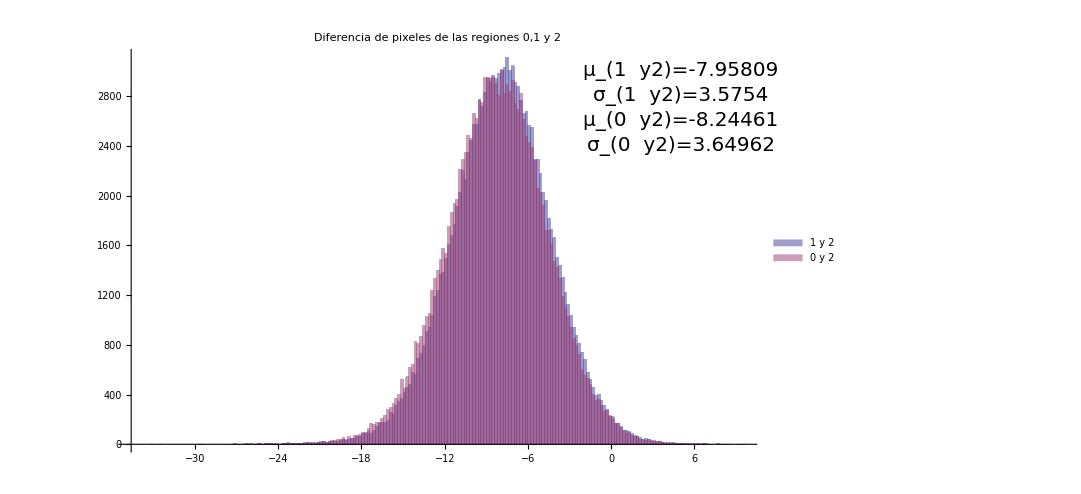

```mathematica
dum=Show[Histogram[{(#[[1,3]]-#[[2,3]])&/@Flatten[res1,1],(#[[1,3]]-#[[2,3]])&/@Flatten[res2,1]},PlotLabel->Style[ "Diferencia de pixeles de las regiones 0,1 y 2",25],ChartLegends->  {"1 y 2","0 y 2"},ImageSize->800],Graphics[{Text[Style["μ_(1  y2)="<>ToString@μ12,20],{5,3000}],Text[Style["σ_(1  y2)="<>ToString@sig12,20],{5,2800}],Text[Style["μ_(0  y2)="<>ToString@μ13,20],{5,2600}],Text[Style["σ_(0  y2)="<>ToString@sig13,20],{5,2400}]}]]
```

```mathematica
Export["./Presentacion/histdif.pdf",dum]
```

./Presentacion/histdif.pdf

```mathematica
512*1024
```

524288

```mathematica
1024/4
```

256

```mathematica
mpi=((#[[1,3]]-#[[2,3]])&/@(Flatten[(Partition[#,2]&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]),1]))//Mean
```

-0.0929396

```mathematica
spi=((#[[1,3]]-#[[2,3]])&/@(Flatten[(Partition[#,2]&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]),1]))//StandardDeviation
```

3.70182

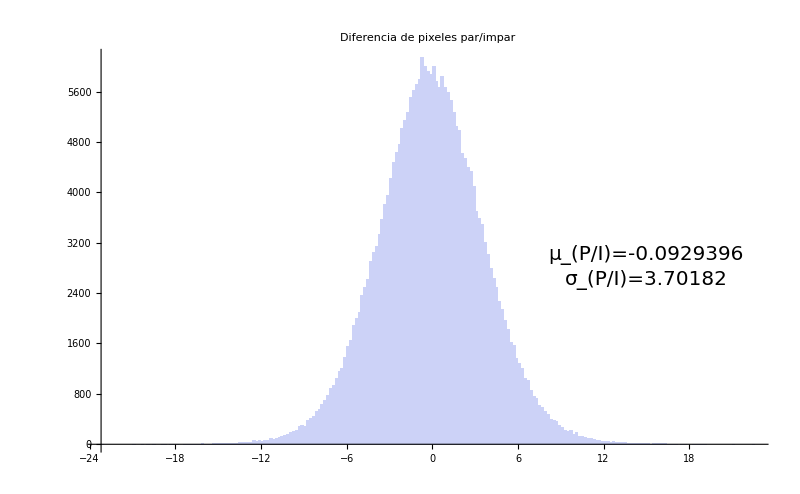

```mathematica
Show[Histogram[(#[[1,3]]-#[[2,3]])&/@(Flatten[(Partition[#,2]&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]),1]),PlotLabel-> Style["Diferencia de pixeles par/impar",25],ImageSize->800],Graphics[{Text[Style["μ_(P/I)="<>ToString@mpi,20],{15,3000}],Text[Style["σ_(P/I)="<>ToString@spi,20],{15,2600}]}]]
```

```mathematica
Export["./Presentacion/histparimp.pdf",%56]
```

./Presentacion/histparimp.pdf

```mathematica
f[x_]:=Module[{dat,res1,res2},
dat=Import["./TEMP"<>x<>"/outputtest0.dat","Data"];
res1=((Partition[#,256][[{2,3}]]//Transpose)&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]);
res2=((Partition[#,256][[{1,3}]]//Transpose)&/@SplitBy[SortBy[Select[dat,Length[#]≠ 1&],#[[2]]&],#[[2]]&]);
Histogram[{(#[[1,3]]-#[[2,3]])&/@Flatten[res1,1],(#[[1,3]]-#[[2,3]])&/@Flatten[res2,1]},PlotLabel->Style[ "Diferencia de pixeles de las regiones 0,1 y 2 a T="<>i,25],ChartLegends-> {"1 y 2","0 y 2"},ImageSize->700]
]
```

```mathematica
ToString/@Range[20,40,5]//FullForm
```

List["20","25","30","35","40"]

```mathematica
temps=Table[f[i],{i,ToString/@Range[20,40,5]}];
```

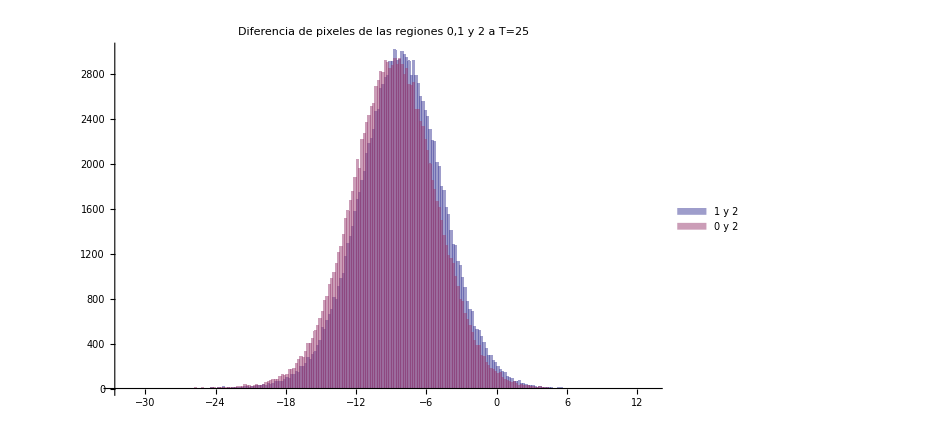
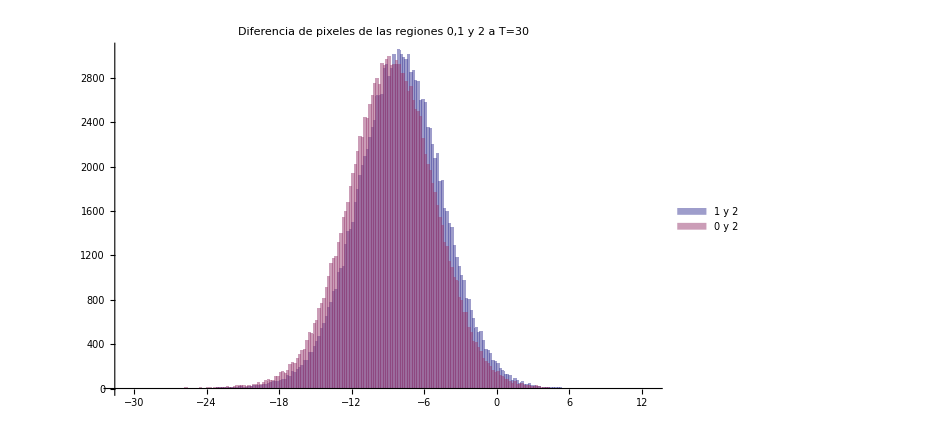
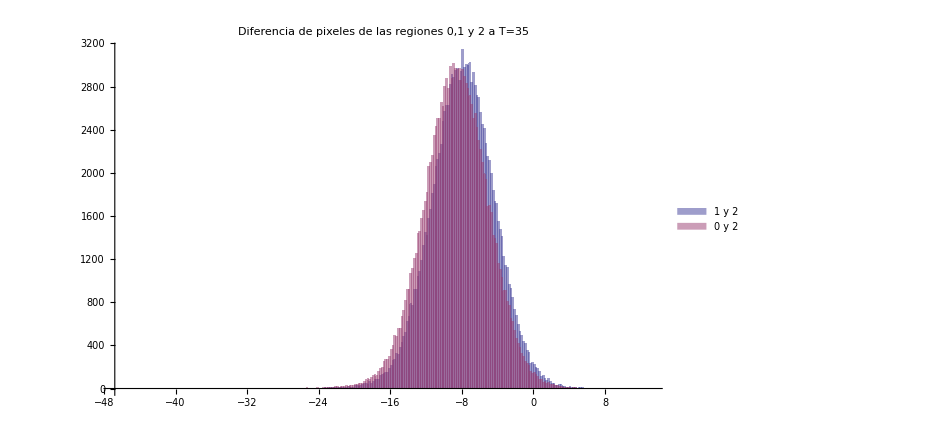
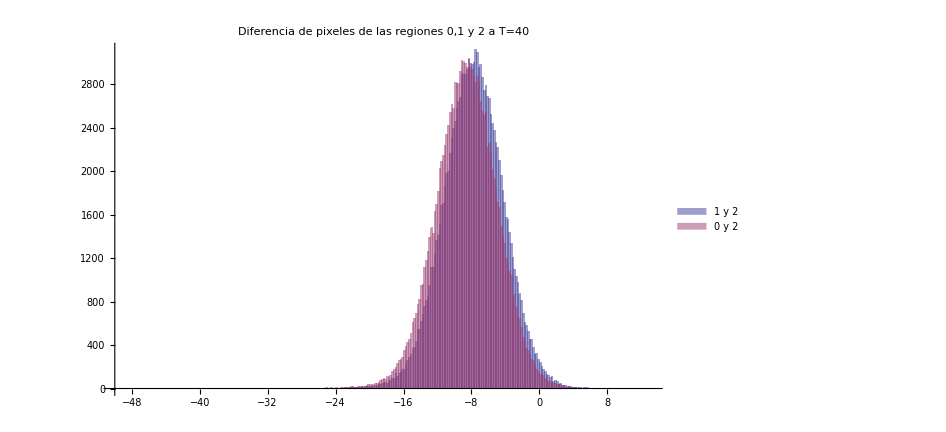

```mathematica
temps//Rest
```

```mathematica
Grid[{{"","Valor 1","Valor 3"},{"Pred. 1",1162,1123},{"Pred. 3",264,451}},Frame->All,Spacings->{2,2}]
```

| Valor 1 | Valor 3
Pred. 1 | 1162 | 1123
Pred. 3 | 264 | 451

```mathematica
Grid[{{"","Valor 1","Valor 3"},{"Pred. 1",1056,389},{"Pred. 3",370,1185}},Frame->All,Spacings->{2,2}]
```

| Valor 1 | Valor 3
Pred. 1 | 1056 | 389
Pred. 3 | 370 | 1185

```mathematica
Grid[{{"","Valor 1","Valor 3"},{"Pred. 1",845,721},{"Pred. 3",581,853}},Frame->All,Spacings->{2,2}]
```

| Valor 1 | Valor 3
Pred. 1 | 845 | 721
Pred. 3 | 581 | 853